# Higgs decay to VV

```mathematica
NotebookEvaluate["/home/bastilo/Dropbox/ProyectoVectorDM/H->Invisible/Definicionesnoi.nb"];
```

Loading FeynCalc from /home/bastilo/.Mathematica/Applications/HighEnergyPhysics

HighEnergyPhysics`FeynCalc`MemoryAvailable`MemoryAvailable::shdw: Symbol MemoryAvailable appears in multiple contexts {HighEnergyPhysics`FeynCalc`MemoryAvailable`,System`}; definitions in context HighEnergyPhysics`FeynCalc`MemoryAvailable` may shadow or be shadowed by other definitions.

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/bastilo/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

## Definiciones

```mathematica
propA[p_,mu_,nu_]:=-I*MetricTensor[mu,nu]/p^2 
propZ[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MZ^2)/(p^2-MZ^2) 
propW[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MW^2)/(p^2-MW^2) 
propVC[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MVC^2)/(p^2-MVC^2) 
propV1[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MV1^2)/(p^2-MV1^2) 
propV2[p_,mu_,nu_]:=-I*(MetricTensor[mu,nu]-(fv[p,mu]*fv[p,nu])/MV2^2)/(p^2-MV2^2) 
pv[k,μ]:=PolarizationVector[k,μ]
```

Amplitude

```mathematica
M=Contract[HV1V1[mu,nu].pv[k1,mu].pv[k2,nu]]
```

-(2 ⅈ λL MW sw g^munu pv(k_1,mu) pv(k_2,nu))/e

```mathematica
HV1V1[mu,nu]
```

-(2 ⅈ λL MW sw g^munu)/e

```mathematica
MC=ComplexConjugate[M]
```

(2 ⅈ λL MW sw g^munu pv(k_1,mu) pv(k_2,nu))/e

```mathematica
MM=Contract[MC.M]
```

(16 λL^2 MW^2 sw^2 (pv(k_1,mu))^2 (pv(k_2,nu))^2)/e^2

Decay width

```mathematica
AHVV=(4π)/(64*π^2*MH)MM*(1/2)
```

-(λL^2 MW^2 sw^2 (g^munu)^2 (pv(k_1,mu))^2 (pv(k_2,nu))^2)/(8 π e^2 MH)

Decay with of the H->V1V1

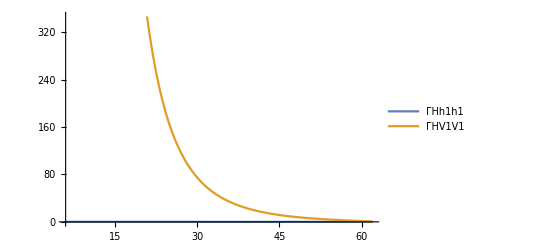

```mathematica
Block[{MW,λL,MH,MV1,g},
MH=125;
MW=90;
λL=0.1;
g=0.6;
ΓHh1h1=(MW^2*λL^2)/(8π*g^2 MH)√(1-(4 MV1^2)/MH^2);

ΓHV1V1=(MW^2*λL^2)/(8π*g^2 MH)(3-MH^2/MV1^2+(4 MH^4)/MV1^4)√(1-(4 MV1^2)/MH^2);
Plot[{ΓHh1h1,ΓHV1V1},{MV1,6,62},PlotLegends->"Expressions"]]
```

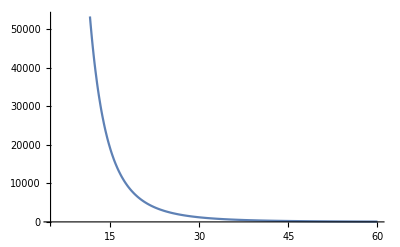

```mathematica
Block[{MW,λL,MH,MV1,g},
MH=125;
MW=90;
λL=1;
g=0.6;
A=(3-MH^2/MV1^2+(4 MH^4)/MV1^4);
Plot[{A},{MV1,5,60},PlotLegends->"Expressions"]]
```

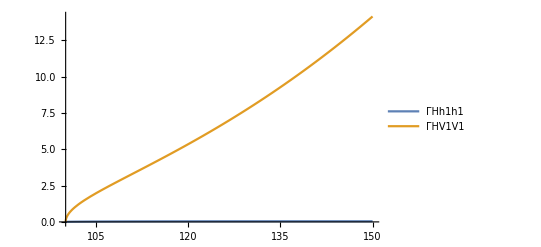

```mathematica
Block[{MW,λL,MH,MV1,g},
MV1=50;
MW=90;
λL=0.1;
g=0.6;
ΓHh1h1=(MW^2*λL^2)/(8π*g^2 MH)√(1-(4 MV1^2)/MH^2);
ΓHV1V1=(MW^2*λL^2)/(8π*g^2 MH)(3-MH^2/MV1^2+(4 MH^4)/MV1^4)√(1-(4 MV1^2)/MH^2);
Plot[{ΓHh1h1,ΓHV1V1},{MH,100,150},PlotLegends->"Expressions"]]
```

```mathematica
Block[{MW,λL,MH,MV1,g},
MH=125;
MW=90;
λL=0.1;
g=0.6;
ΓHh1h1=(MW^2*λL^2)/(8π*g^2 MH)√(1-(4 MV1^2)/MH^2);

ΓHV1V1=(MW^2*λL^2)/(8π*g^2 MH)(3-MH^2/MV1^2+(4 MH^4)/MV1^4)√(1-(4 MV1^2)/MH^2)+(MW^2*λR^2)/(8π*g^2 MH)(3-MH^2/MV1^2+(4 MH^4)/MV2^4)√(1-(4 MV1^2)/MH^2);
Plot[{ΓHh1h1,ΓHV1V1},{MV1,6,62},PlotLegends->"Expressions"]]
```

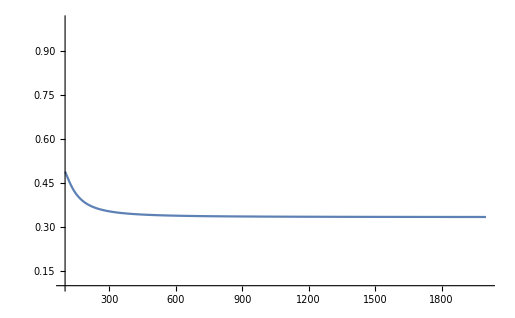

```mathematica
Block[{mh,mv},
mh=125;
Plot[1/(3-(mh/mv)^2+1/4*(mh/mv)^4),{mv,100,2000},PlotRange->{{100.0,2000.0},{0.10,1.0}}]]
```

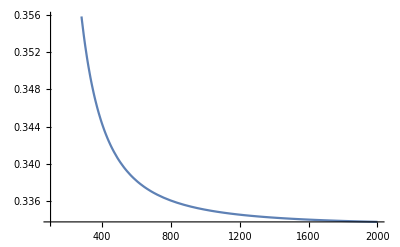

```mathematica
Block[{mh,mv},
mh=125;
Plot[1/(3-(mh/mv)^2+1/4*(mh/mv)^4),{mv,100,2000}]]
```

Plot for λL

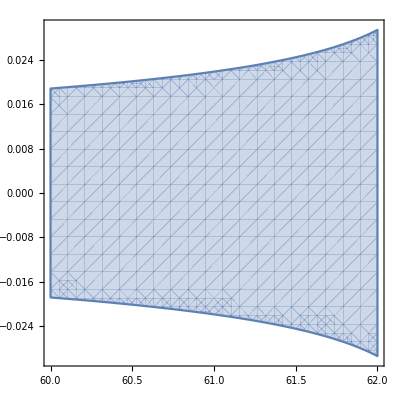

```mathematica
Block[{MH,MV1,g,ΓSM,BR,MW,λL},
MH=125;
g=0.6;
BR=0.24;
ΓSM=6*10^-3;
MW=80;
P024=RegionPlot[Abs[λL]<((8*π*ΓSM*g^2*MH*(1/BR-1)^-1)/(MW^2*(3-(MH/MV1)^2+1/4*(MH/MV1)^4)√(1-4*MV1^2/MH^2)))^(1/2),{MV1,60,62},{λL,-0.03,0.03}]]
```

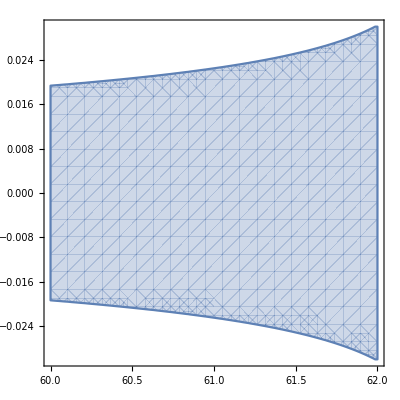

```mathematica
Block[{MH,MV1,g,ΓSM,BR,MW,λL},
MH=125;
g=0.6;
BR=0.25;
ΓSM=6*10^-3;
MW=80;
P025=RegionPlot[Abs[λL]<((8*π*ΓSM*g^2*MH*(1/BR-1)^-1)/(MW^2*(3-(MH/MV1)^2+1/4*(MH/MV1)^4)√(1-4*MV1^2/MH^2)))^(1/2),{MV1,60,62},{λL,-0.03,0.03}]]
```

## Estas son las diferencias entre tomar 0.24 y 0.25 para masas cercanas a 60 GeV

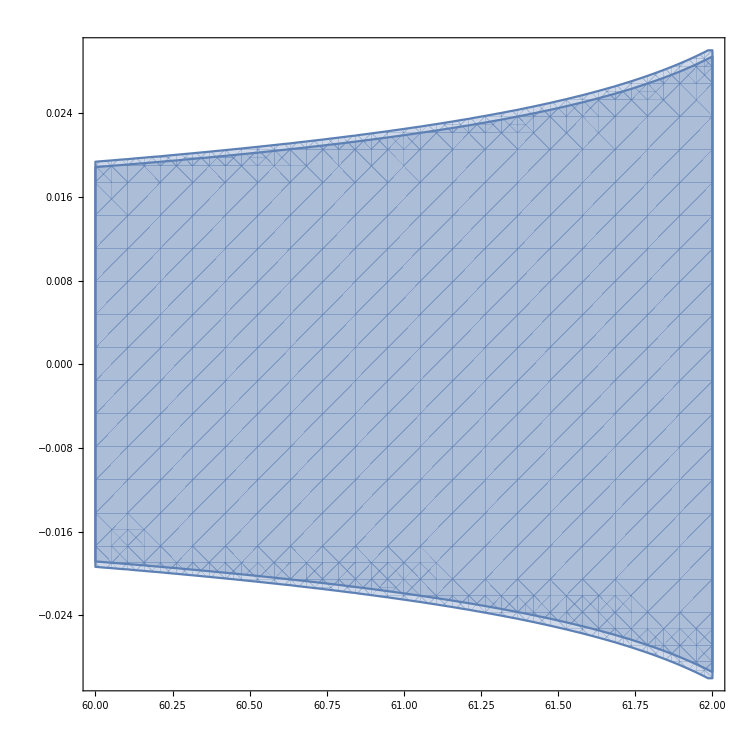

```mathematica
Show[P024,P025]
```

```mathematica
Block[{MH,MV1,g,ΓSM,BR,MW,λL},
MH=125;
g=0.6;
BR=0.10;
ΓSM=6*10^-3;
MW=80;
P010=RegionPlot[Abs[λL]<((8*π*ΓSM*g^2*MH*(1/BR-1)^-1)/(MW^2*(3-(MH/MV1)^2+1/4*(MH/MV1)^4)√(1-4*MV1^2/MH^2)))^(1/2),{MV1,0.1,62},{λL,-0.03,0.03}];]
```

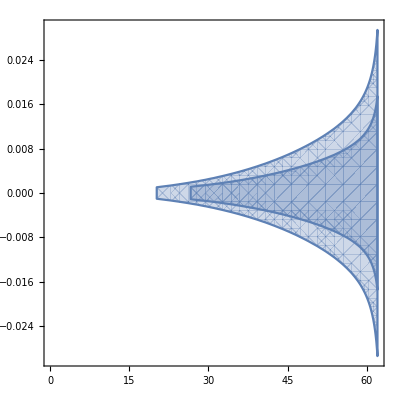

```mathematica
Show[P024,P010]
```